# Figure 1

## Classical Phase space

```mathematica
H[q_,p_,gg_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
V[q_,gg_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
```

#### g=1/2^(1/2)

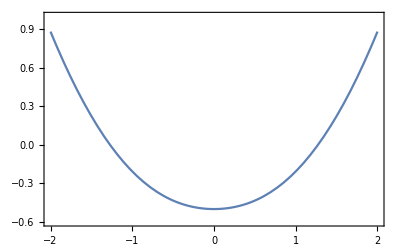

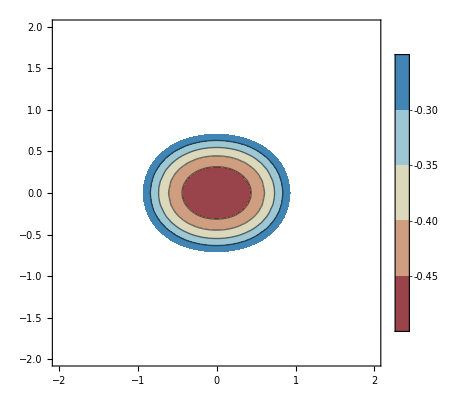

```mathematica
g=1/2^(1/2);
figpot=pot=Show[Plot[V[q,g],{q,-2,2},PlotRange->{{-2,2},{-0.6,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=contour=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.6,-0.25}},LabelStyle->{22,Black},PlotLegends->Automatic,ColorFunction->"RedBlueTones"]
```

#### g=0.95

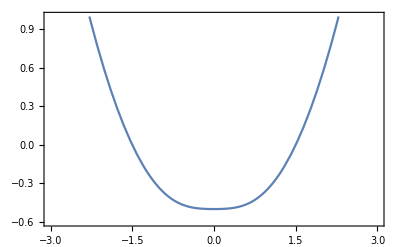

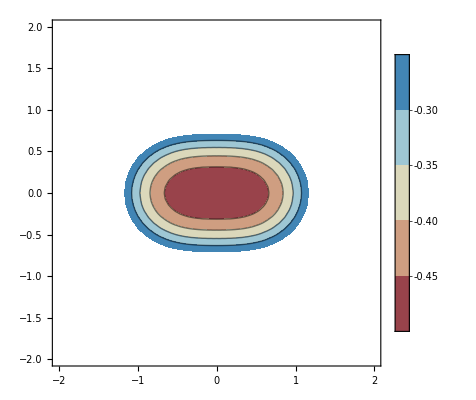

```mathematica
g=0.95;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-0.6,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.65,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=1.05

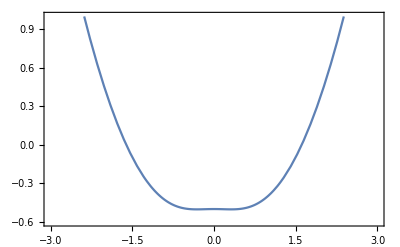

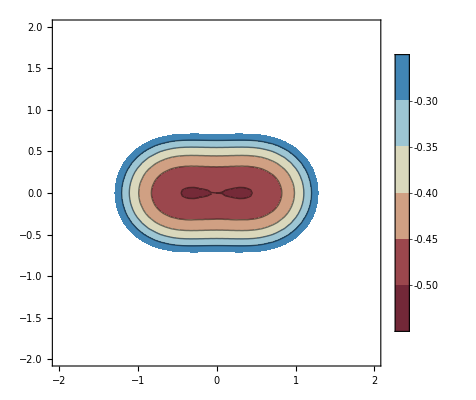

```mathematica
g=1.05;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-0.6,1.0}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.65,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=2^(1/2)

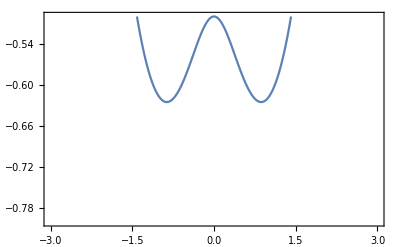

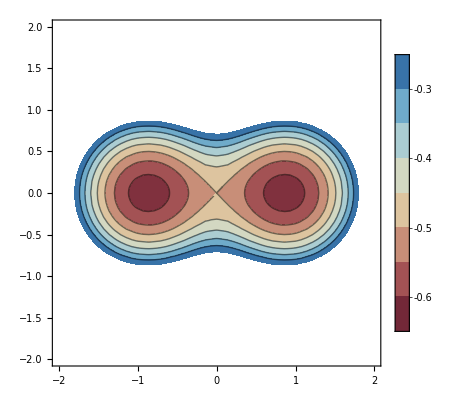

```mathematica
g=2^(1/2);
figpot=Show[Plot[V[q,g],{q,-3,3},Frame->True,Axes->False,PlotRange->{{-3,3},{-0.8,-0.5}},LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.75,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=2

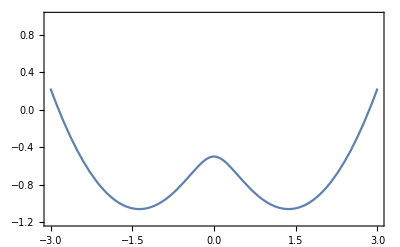

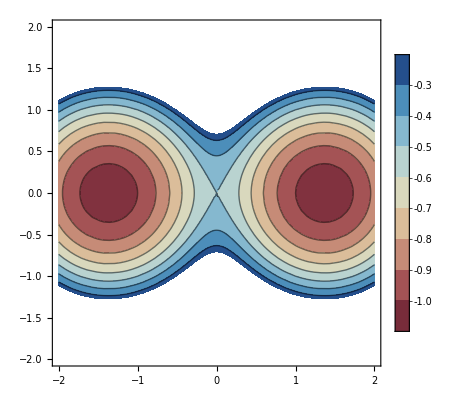

```mathematica
g=2;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-1.2,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-1.25,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},PerformanceGoal->"Accuracy",ColorFunction->"RedBlueTones"]
```

```mathematica
Export["Veff5.png",figpot]
```

Veff5.png

```mathematica
Export["phasespace1.png",figcont]
```

phasespace1.png

## Wigner function

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
datawigner=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/wigner_eig_data.dat"];
datacutw=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/wignercut_eig_data.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
Rr=1/50;
Np=12;
Rd=0.01;
circ=Table[{(Rr+0.01)^(1/2)*Cos[2π*i/Np],(Rr+Rd)^(1/2)*Sin[2π*i/Np]},{i,1,Np}];
```

```mathematica
fac=1;
datawigner2=Table[{datawigner[[i,1]],datawigner[[i,2]],fac*datawigner[[i,3]]},{i,1,Length[datawigner]}];
```

```mathematica
(*Wigner function and Poncaire sections*)figwigner=Show[ListDensityPlot[datawigner2,PlotRange->{{-2,2},{-2,2},All},Frame->  True,FrameTicks->None,ColorFunction->(FCo[1-0.5/0.35 (#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],ListPlot[circ,PlotStyle->{Black,PointSize[0.008]}]]
```

-Graphics-

```mathematica
datacutw1=Table[{datacutw[[i,1]],datacutw[[i,2]]},{i,1,Length[datacutw]}];
datacutw2=Table[{datacutw[[i,3]],datacutw[[i,1]]},{i,1,Length[datacutw]}];
```

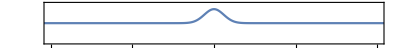

```mathematica
figcut1=ListPlot[datacutw1,Joined->True,PlotRange->{{-2,2},{-0.45,0.45}},Axes->False,FrameTicks->{{None,None},{{-2,-1,0,1,2},None}},Frame->True,LabelStyle->{Black,12},AspectRatio->0.1]
```

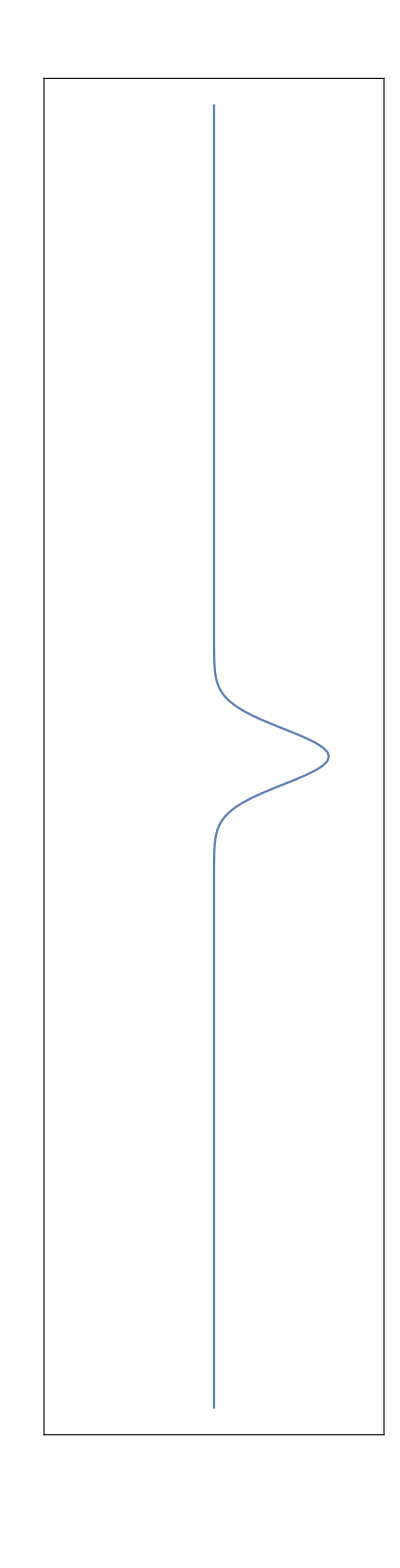

```mathematica
figcut2=ListPlot[datacutw2,Joined->True,PlotRange->{{-0.45,0.45},{-2,2}},Frame->True,FrameTicks->{{None,{-2,-1,0,1,2}},{None,None}},Axes->False,LabelStyle->{Black,12},AspectRatio->9]
```

```mathematica
pad[g_,size_,ip_]:=Show[g,ImageSize->size,PlotRangePadding->None,ImageMargins->0,ImagePadding->ip];

grid=GraphicsGrid[{{pad[figwigner,{700,700},{{8,2},{8,6.5}}],pad[figcut2,{300,710},{{10,25},{10,8}}]},{pad[figcut1,{750,200},{{10,15},{22,6}}],Spacer[{500,200}]}},Spacings->{0,0},Alignment->{Left,Top}]
```

-Graphics-